```mathematica
BigData = Import[
FileNameJoin[{NotebookDirectory[], "Chip1.ply"}],"VertexData"];
Length[BigData]
```

671123

```mathematica
data = DeleteDuplicates[Round[BigData[[1;;-1;;25]]],.01]; (* This takes every other 50 pts*)
Length[data]
dataDim[1] = Sort[Table[data[[i]][[1]],{i,1,Length[data]}]];
dataDim[2]=  Sort[Table[data[[i]][[2]],{i,1,Length[data]}]];
dataDim[3] =  Sort[Table[data[[i]][[3]],{i,1,Length[data]}]];
Table[{Max[dataDim[i]], Min[dataDim[i]]},{i,1,3}]
```

4396

{{37,-1},{-9,-64},{32,13}}

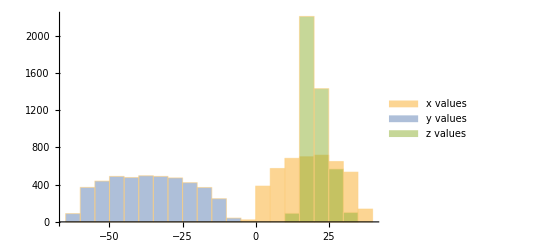

```mathematica
Histogram[{dataDim[1], dataDim[2], dataDim[3]}, ChartLegends->{"x values","y values","z values"}]
```

-Graphics3D-

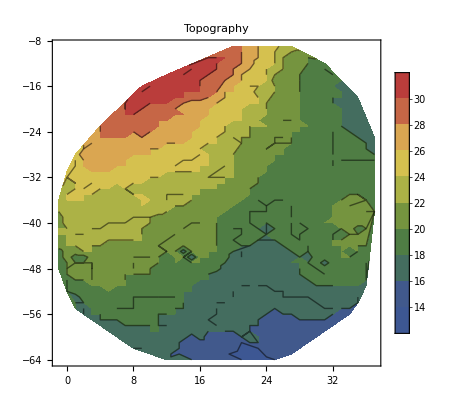

```mathematica
ListPlot3D[data, ColorFunction->"Rainbow", BoxRatios->Automatic,Mesh->None, PlotStyle->{Thickness[50]},PlotLegends->BarLegend[Automatic,LegendMarkerSize->100],PlotLabel->"3D Potato Chip",AxesLabel->{x,y,z},LabelStyle->Bold]

ListContourPlot[data,Mesh->10,PlotRange->All,InterpolationOrder->3,PlotLegends->Automatic, ColorFunction->"DarkRainbow", PlotLabel->"Topography",LabelStyle->Bold]
```

```mathematica
Chip=Interpolation[data, InterpolationOrder->3,"ExtrapolationHandler"->{0&,"WarningMessage"->False}] (*This is a function to create an interpolation of dataset*)
```

Interpolation::indp: There are duplicated abscissa points in ….

Interpolation[{{22,-9,27},{21,-9,28},{23,-9,26},{20,-9,28},{22,-9,26},{24,-9,24},{21,-9,27},{24,-9,25},{20,-9,29},{25,-9,25},{25,-9,23},{21,-10,28},{23,-9,25},{25,-9,24},{23,-10,26},{20,-10,29},{22,-10,27},{19,-10,29},{24,-10,25},{26,-9,23},{25,-10,24},{19,-11,30},{18,-11,30},{21,-11,28},{18,-11,31},4346,{5,-51,19},{3,-52,20},{27,-51,16},{33,-52,18},{8,-52,18},{4,-53,19},{9,-53,19},{29,-53,17},{2,-53,18},{5,-53,18},{3,-56,17},{33,-56,16},{11,-57,17},{32,-57,16},{9,-57,17},{4,-58,18},{14,-58,18},{13,-58,18},{26,-59,16},{16,-60,16},{11,-60,18},{15,-60,17},{15,-61,17},{14,-61,17},{13,-63,17}},1,Ext…dler→1]
 |  |  |  |

```mathematica
Chip[10,-50]
Chip[5,-40]
```

19.1349

20.9382

```mathematica
dataDim[1]=DeleteDuplicates[dataDim[1]];
dataDim[2]=DeleteDuplicates[dataDim[2]];
A = Table[
If[j==1,dataDim[1][[i]],
If[i==1, dataDim[2][[j]],0]],
{i,1,Length[dataDim[1]]}, 
{j,1,Length[dataDim[2]]}]//MatrixForm
```

(1)
 |  |  |  |